# Dimensional Analysis

Peter Cullen Burbery

Abstract

## Section

XXXX:

## Unit and Quantity Input

### Quantity

```mathematica
Quantity[8,"Meters"]
```

8 m

```mathematica
Quantity[4, "Meters"]
```

4 m

```mathematica
Quantity[12, "Kilograms"]
```

```mathematica
Quantity[40, ("Pascals")/("Newtons")]
```

```mathematica
Quantity[1,"Kilograms"]
```

1 kg

```mathematica
Quantity[1.23,("Kilograms""Meters")/"Seconds"]
```

1.23 kg m/s

```mathematica
Quantity[1,"SpeedOfLight"]
```

c

```mathematica
Quantity[, "GravitationalConstant"]
```

```mathematica
3 Quantity[, "MagneticConstant"]
```

3 μ_0

### QuantityArray

```mathematica
QAMETERS=QuantityArray[{2,3,4},"Meters"]
```

QuantityArray[…]

Extract its magnitudes and units separately:

```mathematica
QuantityMagnitude[QAMETERS]
```

{2,3,4}

```mathematica
QuantityUnit[QAMETERS]
```

{Meters,Meters,Meters}

Normalize the quantity array:

```mathematica
Normal[QAMETERS]
```

{2 m,3 m,4 m}

### Quantity Distribution

Define a distribution for a random height:

```mathematica
𝒟=NormalDistribution[,]
```

QuantityDistribution[NormalDistribution[1200,161], mm]

Compute the probability of a certain height range:

```mathematica
Probability[x>Quantity[1540, "Millimeters"],x\[Distributed]𝒟]
```

1/2 (1-Erf[(170 √2)/161])

```mathematica
NProbability[x>Quantity[1540, "Millimeters"],x\[Distributed]𝒟]
```

0.0173518

Define a distribution of life expectancy:

```mathematica
𝒟=GompertzMakehamDistribution[1/,2.56*10^-4,394.,0];
```

Compute conditional life expectancy:

```mathematica
NExpectation[t\[Conditioned]t>Quantity[8, "Decades"],t\[Distributed]𝒟]
```

86.0983 yr

```mathematica
Table[NExpectation[t\[Conditioned]t>n Quantity[1, "Decades"],t\[Distributed]𝒟],{n,10}]
```

{57.3061 yr,61.9519 yr,66.0996 yr,69.7997 yr,73.215 yr,76.6904 yr,80.7782 yr,86.0983 yr,93.002 yr,101.325 yr}

Fit a model to data with units:

```mathematica
times=Quantity[{2.34,1.55,2.7,0.25,1.5,3.5,3.35,1.85,0.15,2.3,0.65,0.85,5.15},"Minutes"];
```

```mathematica
EstimatedDistribution[times,ExponentialDistribution[λ]]
```

QuantityDistribution[ExponentialDistribution[0.497322], min]

Convert the distribution to another compatible unit:

```mathematica
UnitConvert[,"Hours"]
```

QuantityDistribution[ExponentialDistribution[29.8393], h]

Compare with fitting to distribution in hours:

```mathematica
EstimatedDistribution[times,QuantityDistribution[ExponentialDistribution[λ],"Hours"]]
```

QuantityDistribution[ExponentialDistribution[29.8393], h]

## Applications

The average speed of cars traveling from Champaign Illinois to Chicago Illinois is described by a triangular random variable:

```mathematica
speed𝒟=TriangularDistribution[{,},];
```

Find the expected time of travel:

```mathematica
Expectation[GeoDistance[,]/v,v\[Distributed]speed𝒟]
```

2.48738 h

Define the distribution of a cube's side-length measurements:

```mathematica
ℓ𝒟=BatesDistribution[3,{,}]
```

QuantityDistribution[BatesDistribution[3,{235,243}], mm]

Plot the distribution density:

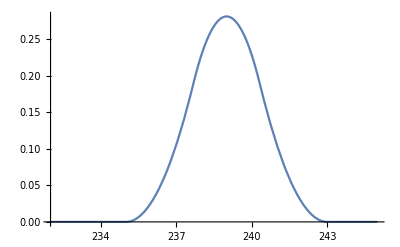

```mathematica
Plot[PDF[ℓ𝒟,Quantity[s,"Millimeters"]]//Evaluate,{s,232,245},Exclusions->None]
```

Compute the mean and the dispersion measures of the cube's volume:

```mathematica
Mean[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]
```

40959581/3 mm^3

```mathematica
Mean[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]//N
```

1.36532×10^7 mm^3

```mathematica
Mean[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]//Round
```

13653194 mm^3

```mathematica
StandardDeviation[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]
```

(4 √(49955519554669/21))/27 mm^3

```mathematica
StandardDeviation[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟]]//Round
```

228496 mm^3

Plot the PDF of the cube's volume:

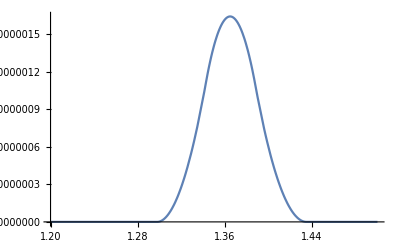

```mathematica
Plot[PDF[TransformedDistribution[s^3,s\[Distributed]ℓ𝒟],Quantity[vol,("Millimeters")^3]]//Evaluate,{vol,1.2*^7 ,1.5*^7},Exclusions->None]
```

Recorded body weights in kilograms:

```mathematica
data=QuantityArray[{67,69,57,78,89,65,57,80,73,66,61,70,64,74,77,69,76,71,75,93,77,78,72,80,63,78,78,52,80,47,70,76,63,77,69,68,48,71,71,69,68,79,67,75,56,62,81,92,63,74,72,90,58,47,58,63,62,73,70,85,61,75,53,59,63,76,78,67,67,83,61,62,75,68,82,65,84,71,49,70,60,72,61,63,84,69,69,52,56,81,78,72,59,67,75,52,67,65,68,60},"Kilograms"];
```

Plot a histogram of the data:

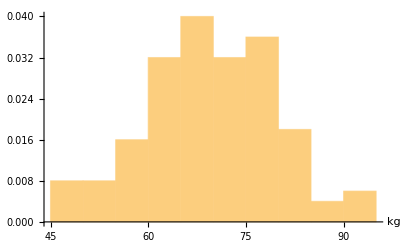

```mathematica
h=Histogram[data,Automatic,"PDF",AxesLabel->Automatic]
```

## Units and Prefixes

```mathematica
EntityRegister[SIPREFIXES=EntityStore["SI prefixes"-><|"Entities"-><|3-><|"Factor"->10^3,"Name"->"kilo","Symbol"->"k"|>,6-><|"Factor"->10^6,"Name"->"mega","Symbol"->"M"|>,9-><|"Factor"->10^9,"Name"->"giga","Symbol"->"G"|>,12-><|"Factor"->10^12,"Name"->"tera","Symbol"->"T"|>,15-><|"Factor"->10^15,"Name"->"peta","Symbol"->"P"|>,18-><|"Factor"->10^18,"Name"->"exa","Symbol"->"E"|>,
21-><|"Factor"->10^21,"Name"->"zetta","Symbol"->"Z"|>,
24-><|"Factor"->10^24,"Name"->"yotta","Symbol"->"Y"|>,
27-><|"Factor"->10^27,"Name"->"ronna","Symbol"->"R"|>,
30-><|"Factor"->10^30,"Name"->"quetta","Symbol"->"Q"|>,
-3-><|"Factor"->10^-3,"Name"->"milli","Symbol"->"m"|>,-6-><|"Factor"->10^-6,"Name"->"micro","Symbol"->"μ"|>,-9-><|"Factor"->10^-9,"Name"->"nano","Symbol"->"n"|>,-12-><|"Factor"->10^-12,"Name"->"pico","Symbol"->"p"|>,-15-><|"Factor"->10^-15,"Name"->"femto","Symbol"->"f"|>,-18-><|"Factor"->10^-18,"Name"->"atto","Symbol"->"a"|>,
-21-><|"Factor"->10^-21,"Name"->"zepto","Symbol"->"z"|>,
-24-><|"Factor"->10^-24,"Name"->"yocto","Symbol"->"y"|>,
-27-><|"Factor"->10^-27,"Name"->"ronto","Symbol"->"r"|>,
-30-><|"Factor"->10^-30,"Name"->"quecto","Symbol"->"q"|>|>|>]]
```

{SI prefixes}

```mathematica
EntityList["SI prefixes"]
```

{3,6,9,12,15,18,21,24,27,30,-3,-6,-9,-12,-15,-18,-21,-24,-27,-30}

```mathematica
#["Dataset"]&/@EntityList["SI prefixes"]
```

{,,,,,,,,,,,,,,,,,,,}

```mathematica
Quit
```

```mathematica
EntityRegister[NONSIUNITSACCEPTEDFORUSEWITHTHESIUNITS=EntityStore["Non-SI units accepted for use with the SI units"-><|"Entities"-><|"minute"-><|"Quantity"->"time","Symbol for unit"->"min","Value in SI units"->Quantity[60,"Seconds"]|>,"hour"-><|"Quantity"->"time","Symbol for unit"->"h","Value in SI units"->Quantity[3600,"Seconds"]|>,"day"-><|"Quantity"->"time","Symbol for unit"->"d","Value in SI units"->Quantity[86400,"Seconds"]|>,"astronomical unit"-><|"Quantity"->"length plane and phase angle","Symbol for unit"->"au","Value in SI units"->Quantity[149597870700,"Meters"]|>
,"degree"-><|"Quantity"->"length plane and phase angle","Symbol for unit"->"°","Value in SI units"->Pi/180|>
,"minute"-><|"Quantity"->"length plane and phase angle","Symbol for unit"->"′","Value in SI units"->Pi/10800|>,"second"-><|"Quantity"->"length plane and phase angle","Symbol for unit"->"″","Value in SI units"->Pi/648000|>,"hectare"-><|"Quantity"->"area","Symbol for unit"->"ha","Value in SI units"->Quantity[10000,("Meters")^2]|>,"liter"-><|"Quantity"->"volume","Symbol for unit"->"L","Value in SI units"->Quantity[10^-3,("Meters")^3]|>,"metric ton"-><|"Quantity"->"mass","Symbol for unit"->"t","Value in SI units"->Quantity[10^3,"Kilograms"]|>,"dalton"-><|"Quantity"->"mass","Symbol for unit"->"Da","Value in SI units"->Quantity[1,"Daltons"]|>,"electronvolt"-><|"Quantity"->"energy","Symbol for unit"->"eV","Value in SI units"->Quantity[1,"Electronvolts"]|>|>|>]]
```

{Non-SI units accepted for use with the SI units}

```mathematica
EntityUnregister[NONSIUNITSACCEPTEDFORUSEWITHTHESIUNITS]
```

```mathematica
Column[#["Dataset"]&/@EntityList["Non-SI units accepted for use with the SI units"]]
```

## Dimensional analysis

```mathematica
SEVENCONSTANTS=<|"Hyper"|>
```

```mathematica
store=EntityStore["Seven defining constants of the SI"-><|
"Entities"-><|
"hyperfine transition frequency of Cs"-><|"Symbol"->"Δν_Cs","Numerical value"->9192631770,"Unit"->"Hz"|>,
"speed of light in vacuum"-><|"Symbol"->"c","Numerical value"->299458792,"Unit"->"m s^-1"|>,"Planck constant"-><|"Symbol"->"h","Numerical value"->6.62607015 10^-34,"Unit"->"J s"|>,"elementary charge"-><|"Symbol"->"e","Numerical value"->1.602176634 10^-19,"Unit"->"C"|>,"Boltzmann constant"-><|"Symbol"->"k","Numerical value"->1.380649 10^-23,"Unit"->"J K^-1"|>,"Avogadro constant"-><|"Symbol"->"N_A","Numerical value"->6.02214076 10^23,"Unit"->"mol^-1"|>,"luminous efficacy"-><|"Symbol"->"K_cd","Numerical value"->683,"Unit"->"lm W^-1"|>
|>
|>]
```

EntityStore[…]

```mathematica
EntityRegister[store]
```

{Seven defining constants of the SI}

```mathematica
InputForm[{"Seven defining constants of the SI"}]
```

{"Seven defining constants of the SI"}

```mathematica
EntityList[First[InputForm[{"Seven defining constants of the SI"}]]]
```

{Seven defining constants of the SI}

```mathematica
Entity["Seven defining constants of the SI","Boltzmann constant"]
```

Boltzmann constant

```mathematica
EntityUnregister[store]
```

```mathematica
EntityUnregister["Seven defining constants of the SI"]
```

```mathematica
Entity["Seven defining constants of the SI","Boltzmann constant"]
```

Entity[Seven defining constants of the SI,Boltzmann constant]

```mathematica
Entity["Seven defining constants of the SI","Boltzmann constant"]["Properties"]
```

{Symbol}

```mathematica
Entity["Seven defining constants of the SI","Boltzmann constant"]["Dataset"]
```

```mathematica
EntityList["Seven defining constants of the SI"]
```

{hyperfine transition frequency of Cs,speed of light in vacuum,Planck constant,elementary charge,Boltzmann constant,Avogadro constant,luminous efficacy}

```mathematica
EntityValue[#,"Dataset"]&/@EntityList["Seven defining constants of the SI"]
```

{,,,,,,}

```mathematica
EntityValue[#,"PropertyAssociation"]&/@EntityList["Seven defining constants of the SI"]
```

{<|Numerical value→9192631770,Symbol→Δν_Cs,Unit→Hz|>,<|Numerical value→299458792,Symbol→c,Unit→m s^-1|>,<|Numerical value→6.62607×10^-34,Symbol→h,Unit→J s|>,<|Numerical value→1.60218×10^-19,Symbol→e,Unit→C|>,<|Numerical value→1.38065×10^-23,Symbol→k,Unit→J K^-1|>,<|Numerical value→6.02214×10^23,Symbol→N_A,Unit→mol^-1|>,<|Numerical value→683,Symbol→K_cd,Unit→lm W^-1|>}

```mathematica
(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]
```

{hyperfine transition frequency of Cs→<|Numerical value→9192631770,Symbol→Δν_Cs,Unit→Hz|>,speed of light in vacuum→<|Numerical value→299458792,Symbol→c,Unit→m s^-1|>,Planck constant→<|Numerical value→6.62607×10^-34,Symbol→h,Unit→J s|>,elementary charge→<|Numerical value→1.60218×10^-19,Symbol→e,Unit→C|>,Boltzmann constant→<|Numerical value→1.38065×10^-23,Symbol→k,Unit→J K^-1|>,Avogadro constant→<|Numerical value→6.02214×10^23,Symbol→N_A,Unit→mol^-1|>,luminous efficacy→<|Numerical value→683,Symbol→K_cd,Unit→lm W^-1|>}

```mathematica
Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]]
```

<|hyperfine transition frequency of Cs→<|Numerical value→9192631770,Symbol→Δν_Cs,Unit→Hz|>,speed of light in vacuum→<|Numerical value→299458792,Symbol→c,Unit→m s^-1|>,Planck constant→<|Numerical value→6.62607×10^-34,Symbol→h,Unit→J s|>,elementary charge→<|Numerical value→1.60218×10^-19,Symbol→e,Unit→C|>,Boltzmann constant→<|Numerical value→1.38065×10^-23,Symbol→k,Unit→J K^-1|>,Avogadro constant→<|Numerical value→6.02214×10^23,Symbol→N_A,Unit→mol^-1|>,luminous efficacy→<|Numerical value→683,Symbol→K_cd,Unit→lm W^-1|>|>

```mathematica
Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]]]
```

```mathematica
BASEUNITS=
```

```mathematica
EntityStore["t"-><|"Entities"->Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]]|>]
```

EntityStore[…]

```mathematica
EntityRegister[EntityStore["t"-><|"Entities"->Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Seven defining constants of the SI"]]|>]]
```

{t}

```mathematica
EntityList["t"]
```

{hyperfine transition frequency of Cs,speed of light in vacuum,Planck constant,elementary charge,Boltzmann constant,Avogadro constant,luminous efficacy}

```mathematica
Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["t"]]]
```

```mathematica
Normal[Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["t"]]]]
```

<|hyperfine transition frequency of Cs→<|Numerical value→9192631770,Symbol→Δν_Cs,Unit→Hz|>,speed of light in vacuum→<|Numerical value→299458792,Symbol→c,Unit→m s^-1|>,Planck constant→<|Numerical value→6.62607×10^-34,Symbol→h,Unit→J s|>,elementary charge→<|Numerical value→1.60218×10^-19,Symbol→e,Unit→C|>,Boltzmann constant→<|Numerical value→1.38065×10^-23,Symbol→k,Unit→J K^-1|>,Avogadro constant→<|Numerical value→6.02214×10^23,Symbol→N_A,Unit→mol^-1|>,luminous efficacy→<|Numerical value→683,Symbol→K_cd,Unit→lm W^-1|>|>

```mathematica
EntityUnregister["t"]
```

```mathematica
Normal[Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["t"]]]]
```

Association[(#1→EntityValue[#1,PropertyAssociation]&)/@EntityList[t]]

```mathematica
SEVENDEFININGCONSTANTSOFTHESIANDTHESEVENCORRESPONDINGUNITSTHEYDEFINE=EntityStore["Seven defining constants of the SI"-><|
"Entities"-><|
"hyperfine transition frequency of Cs"-><|"Symbol"->"Δν_Cs","Numerical value"->9192631770,"Unit"->"Hz"|>,
"speed of light in vacuum"-><|"Symbol"->"c","Numerical value"->299458792,"Unit"->"m s^-1"|>,"Planck constant"-><|"Symbol"->"h","Numerical value"->6.62607015 10^-34,"Unit"->"J s"|>,"elementary charge"-><|"Symbol"->"e","Numerical value"->1.602176634 10^-19,"Unit"->"C"|>,"Boltzmann constant"-><|"Symbol"->"k","Numerical value"->1.380649 10^-23,"Unit"->"J K^-1"|>,"Avogadro constant"-><|"Symbol"->"N_A","Numerical value"->6.02214076 10^23,"Unit"->"mol^-1"|>,"luminous efficacy"-><|"Symbol"->"K_cd","Numerical value"->683,"Unit"->"lm W^-1"|>
|>
|>]
```

EntityStore[…]

```mathematica
SIBASEUNITS=EntityStore["SI Base Units"-><|"Entities"-><|"second"-><|"Base Quantity Name"->"time","Base Quantity Typical Symbol"->"t","Base Unit Name"->"second","Base Unit Symbol"->"s"|>,"meter"-><|"Base Quantity Name"->"length","Base Quantity Typical Symbol"->"l,x,r,etc.","Base Unit Name"->"meter","Base Unit Symbol"->"m" |>,"kilogram"-><|"Base Quantity Name"->"mass","Base Quantity Typical Symbol"->"m","Base Unit Name"->"kilogram","Base Unit Symbol"->"kg"|>,"ampere"-><|"Base Quantity Name"->"electric current","Base Quantity Typical Symbol"->"I,i","Base Unit Name"->"ampere","Base Unit Symbol"->"A"|>,"kelvin"-><|"Base Quantity Name"->"thermodynamic temperature","Base Quantity Typical Symbol"->"T","Base Unit Name"->"kelvin","Base Unit Symbol"->"K"|>,"mole"-><|"Base Quantity Name"->"amount of substance","Base Quantity Typical Symbol"->"n","Base Unit Name"->"mole","Base Unit Symbol"->"mol"|>,"candela"-><|"Base Quantity Name"->"luminous intensity","Base Quantity Typical Symbol"->"I_ν","Base Unit Name"->"candela","Base Unit Symbol"->"cd"|>|>|>]
```

EntityStore[…]

```mathematica
EntityRegister[SIBASEUNITS=EntityStore["SI Base Units"-><|"Entities"-><|"second"-><|"Base Quantity Name"->"time","Base Quantity Typical Symbol"->"t","Base Unit Name"->"second","Base Unit Symbol"->"s"|>,"meter"-><|"Base Quantity Name"->"length","Base Quantity Typical Symbol"->"l,x,r,etc.","Base Unit Name"->"meter","Base Unit Symbol"->"m" |>,"kilogram"-><|"Base Quantity Name"->"mass","Base Quantity Typical Symbol"->"m","Base Unit Name"->"kilogram","Base Unit Symbol"->"kg"|>,"ampere"-><|"Base Quantity Name"->"electric current","Base Quantity Typical Symbol"->"I,i","Base Unit Name"->"ampere","Base Unit Symbol"->"A"|>,"kelvin"-><|"Base Quantity Name"->"thermodynamic temperature","Base Quantity Typical Symbol"->"T","Base Unit Name"->"kelvin","Base Unit Symbol"->"K"|>,"mole"-><|"Base Quantity Name"->"amount of substance","Base Quantity Typical Symbol"->"n","Base Unit Name"->"mole","Base Unit Symbol"->"mol"|>,"candela"-><|"Base Quantity Name"->"luminous intensity","Base Quantity Typical Symbol"->"I_ν","Base Unit Name"->"candela","Base Unit Symbol"->"cd"|>|>|>]]
```

{SI Base Units}

```mathematica
Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["SI Base Units"]]]
```

```mathematica
EntityRegister[BASEQUANTITIESANDDIMENSIONSUSEDINTHESI=EntityStore["Base quantities and dimensions used in the SI"-><|"Entities"-><|"time"-><|"Typical symbol for quantity"->"t","Symbol for dimension"->"T"|>,"length"-><|"Typical symbol for quantity"->"l,x,r,etc.","Symbol for dimension"->"L"|>,"mass"-><|"Typical symbol for quantity"->"m","Symbol for dimension"->"M"|>,"electric current"-><|"Typical symbol for quantity"->"I,i","Symbol for dimension"->"I"|>,"thermodynamic temperature"-><|"Typical symbol for quantity"->"T","Symbol for dimension"->"Θ"|>,"amount of substance"-><|"Typical symbol for quantity"->"n","Symbol for dimension"->"N"|>,"luminous intensity"-><|"Typical symbol for quantity"->"I_v","Symbol for dimension"->"J"|>|>|>]]
```

{Base quantities and dimensions used in the SI}

```mathematica
EntityUnregister["Base quantities and dimensions used in the SI"]
```

```mathematica
Entity["Base quantities and dimensions used in the SI", "time"]
```

time

```mathematica
AssociationMap[{Entity["Base quantities and dimensions used in the SI", "time"][#]}&,Entity["Base quantities and dimensions used in the SI", "time"]["Properties"]]
```

<|Symbol for dimension→{T},Typical symbol for quantity→{t}|>

```mathematica
PersistResourceFunction[{"PhysicalQuantityData"}];
```

```mathematica
PhysicalQuantityData["Time"]
```

[Time]

```mathematica
Entity["PhysicalQuantity","Time"]
```

time

```mathematica
Entity["PhysicalQuantity","Time"]["PropertyAssociation"]
```

<|abbreviations→Missing[NotAvailable],algebraic types→{positive real,scalar},alternate names→Missing[NotAvailable],base physical quantity→Missing[NotAvailable],canonical unit→1 s,classes→{SI base quantities},dimensions→{{TimeUnit,1}},entity classes→{SI base quantities},instances→{characteristic time,data transfer time,downtime,elapsed real time,lag,latency,moving time,ping time,Poincaré recurrence time,relaxation time,reverberation time,round-trip delay,time difference,time shift,uptime,working time},name→time,named SI unit→1 s,physical property type→Missing[NotApplicable],quantity variable→t Time,SI base unit→1 s,SI unit→1 s,standard identifiers→<|ISO 31/I-1978→1-6.1,ISO 31-1:1992→1-7,ISO 80000-3:2006→3-7,ISO 80000-3:2019→3-9,Wikidata→Q2199864|>,standard symbols→<|ISO→{t},Wikidata→{t,Δt}|>,symbols→{t,Δt}|>

```mathematica
Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Base quantities and dimensions used in the SI"]]]
```

```mathematica
EntityRegister[THE22SIUNITSWITHSPECIALNAMESANDSYMBOLS=EntityStore["SI units with special names and symbols"-><|"Entities"-><|"radian"-><|"Derived quantity"->"plane angle","Special name of unit"->"radian","Unit expressed in terms of base units"->"rad=m/m","Unit expressed in terms of other SI units"->""|>,"steradian"-><|"Derived quantity"->"solid angle","Special name of unit"->"steradian","Unit expressed in terms of base units"->"sr=m^2/m^2","Unit expressed in terms of other SI units"->""|>,"hertz"-><|"Derived quantity"->"frequency","Special name of unit"->"hertz","Unit expressed in terms of base units"->"Hz=s^-1","Unit expressed in terms of other SI units"->""|>,"newton"-><|"Derived quantity"->"force","Special name of unit"->"netwon","Unit expressed in terms of base units"->"N=kg m s^-2","Unit expressed in terms of other SI units"->""|>,"pascal"-><|"Derived quantity"->"pressure, stress","Special name of unit"->"pascal","Unit expressed in terms of base units"->"Pa=kg m^-1 s^-2","Unit expressed in terms of other SI units"->""|>,"joule"-><|"Derived quantity"->"energy, work, amount of heat","Special name of unit"->"joule","Unit expressed in terms of base units"->"J=kg m^2 s^-2","Unit expressed in terms of other SI units"->"N m"|>,"watt"-><|"Derived quantity"->"power, radiant flux","Special name of unit"->"watt","Unit expressed in terms of base units"->"W=kg m^2 s^-3","Unit expressed in terms of other SI units"->"J/s"|>,"coulomb"-><|"Derived quantity"->"electric charge","Special name of unit"->"coulomb","Unit expressed in terms of base units"->"C=A s","Unit expressed in terms of other SI units"->""|>,"volt"-><|"Derived quantity"->"electric potential difference","Special name of unit"->"volt","Unit expressed in terms of base units"->"V=kg m^2 s^-3 A^-1","Unit expressed in terms of other SI units"->"W/A"|>,"farad"-><|"Derived quantity"->"capacitance","Special name of unit"->"farad","Unit expressed in terms of base units"->"F=kg^-1 m^2 s^4 A^2","Unit expressed in terms of other SI units"->"C/V"|>,"ohm"-><|"Derived quantity"->"electric resistance","Special name of unit"->"ohm","Unit expressed in terms of base units"->"Ω=kg m^2 s^-3 A^-2","Unit expressed in terms of other SI units"->"V/A"|>,"siemens"-><|"Derived quantity"->"electric conductance","Special name of unit"->"siemens","Unit expressed in terms of base units"->"S=kg^-1 m^-2 s^3 A^2","Unit expressed in terms of other SI units"->"A/V"|>,"weber"-><|"Derived quantity"->"magnetic flux","Special name of unit"->"weber","Unit expressed in terms of base units"->"Wb=kg m^2 s^-2 A^-1","Unit expressed in terms of other SI units"->"V s"|>,"tesla"-><|"Derived quantity"->"magnetic flux density","Special name of unit"->"tesla","Unit expressed in terms of base units"->"T=kg s^-2 A^-1","Unit expressed in terms of other SI units"->"Wb/m^2"|>,"henry"-><|"Derived quantity"->"inductance","Special name of unit"->"henry","Unit expressed in terms of base units"->"H=kg m^2 s^-2 A^-2","Unit expressed in terms of other SI units"->"Wb/A"|>,"degree Celsius"-><|"Derived quantity"->"Celsius temperature","Special name of unit"->"degrees Celsius","Unit expressed in terms of base units"->"°C=K","Unit expressed in terms of other SI units"->""|>,"lumen"-><|"Derived quantity"->"luminous flux","Special name of unit"->"lumen","Unit expressed in terms of base units"->"lm=cd sr","Unit expressed in terms of other SI units"->"cd sr"|>,"lux"-><|"Derived quantity"->"illuminance","Special name of unit"->"lux","Unit expressed in terms of base units"->"lx=cd sr m^-2","Unit expressed in terms of other SI units"->"lm/m^2"|>,"becquerel"-><|"Derived quantity"->"activity referred to a radionuclide","Special name of unit"->"becquerel","Unit expressed in terms of base units"->"Bq=s^-1","Unit expressed in terms of other SI units"->""|>,"gray"-><|"Derived quantity"->"absored dose, kerma","Special name of unit"->"gray","Unit expressed in terms of base units"->"Gy=m^2 s^-2","Unit expressed in terms of other SI units"->"J/kg"|>,"sievert"-><|"Derived quantity"->"dose equivalent","Special name of unit"->"sievert","Unit expressed in terms of base units"->"Sv=m^2 s^-2","Unit expressed in terms of other SI units"->"J/kg"|>,"katal"-><|"Derived quantity"->"catalytic activity","Special name of unit"->"katal","Unit expressed in terms of base units"->"kat=mol s^-1","Unit expressed in terms of other SI units"->""|>|>|>]]
```

{SI units with special names and symbols}

```mathematica
Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["SI units with special names and symbols"]]]
```

```mathematica
EntityRegister[EXAMPLESOFCOHERENTDERIVEDUNITSINTHESIEXPRESSEDINTERMSOFBASEUNITS=EntityStore["Examples of coherent derived units in the SI expressed in terms of base units"-><|"Entities"-><|"area"-><|"Derived quantity"->"area","Typical symbol or quantity"->"A","Derived unit expressed in terms of base units"->"m^2"|>,"volume"-><|"Derived quantity"->"volume","Typical symbol or quantity"->"V","Derived unit expressed in terms of base units"->"m^3"|>,"speed, velocity"-><|"Derived quantity"->"speed, velocity","Typical symbol or quantity"->"v","Derived unit expressed in terms of base units"->"m s^-1"|>,"acceleration"-><|"Derived quantity"->"acceleration","Typical symbol or quantity"->"a","Derived unit expressed in terms of base units"->"m s^-2"|>,"wavenumber"-><|"Derived quantity"->"wavenumber","Typical symbol or quantity"->"σ","Derived unit expressed in terms of base units"->"m^-1"|>,"density, mass density"-><|"Derived quantity"->"density, mass density","Typical symbol or quantity"->"ρ","Derived unit expressed in terms of base units"->"kg m^-3"|>,"surface density"-><|"Derived quantity"->"surface density","Typical symbol or quantity"->"ρ_A","Derived unit expressed in terms of base units"->"kg m^-2"|>,"specific volume"-><|"Derived quantity"->"specific volume","Typical symbol or quantity"->"v","Derived unit expressed in terms of base units"->"m^3 kg^-1"|>,"current density"-><|"Derived quantity"->"current density","Typical symbol or quantity"->"j","Derived unit expressed in terms of base units"->"A m^-2"|>,"magnetic field strength"-><|"Derived quantity"->"magnetic field strength","Typical symbol or quantity"->"H","Derived unit expressed in terms of base units"->"A m^-1"|>,"amount of substance concentration"-><|"Derived quantity"->"amount of substance concentration","Typical symbol or quantity"->"A","Derived unit expressed in terms of base units"->"mol m^-3"|>,"mass concentration"-><|"Derived quantity"->"mass concentration","Typical symbol or quantity"->"ρ,γ","Derived unit expressed in terms of base units"->"kg m^-3"|>,"luminance"-><|"Derived quantity"->"luminance","Typical symbol or quantity"->"L_v","Derived unit expressed in terms of base units"->"cd m^-2"|>|>|>]]
```

{Examples of coherent derived units in the SI expressed in terms of base units}

```mathematica
Dataset[Association[(#->EntityValue[#,"PropertyAssociation"])&/@EntityList["Examples of coherent derived units in the SI expressed in terms of base units"]]]
```

```mathematica
Quit
```

```mathematica
EntityRegister[EXAMPLESOFSICOHERENTDERIVEDUNITSWHOSENAMESANDSYMBOLSINCLUDESICOHERENTDERIVEDUNITSWITHSPECIALNAMESANDSYMBOLS=EntityStore["Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols"-><|"Entities"-><|"dynamic viscosity"-><|"Derived quantity"->"dynamic viscosity","Name of coherent derived unit"->"pascal second","Symbol"->"Pa s","Derived unit expressed in terms of base units"->"kg m^-1 s^-1"|>,"moment of force"-><|"Derived quantity"->"moment of force","Name of coherent derived unit"->"newton meter","Symbol"->"N m","Derived unit expressed in terms of base units"->"kg m^2 s^-2"|>,"surface tension"-><|"Derived quantity"->"surface tension","Name of coherent derived unit"->"newton per meter","Symbol"->"N m^-1","Derived unit expressed in terms of base units"->"kg s^-1"|>,"angular velocity, angular frequency"-><|"Derived quantity"->"angular velocity, angular frequency","Name of coherent derived unit"->"radian per second","Symbol"->"rad s^-1","Derived unit expressed in terms of base units"->"s^-1"|>,"angular acceleration"-><|"Derived quantity"->"angular acceleration","Name of coherent derived unit"->"radian per second squared","Symbol"->"rad/s^2","Derived unit expressed in terms of base units"->"s^-2"|>,"heat flux density, irradiance"-><|"Derived quantity"->"heat flux density, irradiance","Name of coherent derived unit"->"watt per square meter","Symbol"->"W/m^2","Derived unit expressed in terms of base units"->"kg s^-3"|>,"heat capacity, entropy"-><|"Derived quantity"->"heat capacity, entropy","Name of coherent derived unit"->"joule per kelvin","Symbol"->"J K^-1","Derived unit expressed in terms of base units"->"kg m^2 s^-2 K^-1"|>,"specific heat capacity, specific entropy"-><|"Derived quantity"->"specific heat capacity, specific entropy","Name of coherent derived unit"->"joule per kilogram kelvin","Symbol"->"J K^-1 kg^-1","Derived unit expressed in terms of base units"->"m^2 s^-2 K^-1"|>,"specific energy"-><|"Derived quantity"->"specific energy","Name of coherent derived unit"->"joule per kilogram","Symbol"->"J kg^-1","Derived unit expressed in terms of base units"->"m^2 s^-2"|>,"thermal conductivity"-><|"Derived quantity"->"thermal conductivity","Name of coherent derived unit"->"watt per meter kelvin","Symbol"->"W m^-1 K^-1","Derived unit expressed in terms of base units"->"kg m s^-3 K^-1"|>,"energy density"-><|"Derived quantity"->"energy density","Name of coherent derived unit"->"joule per cubic meter","Symbol"->"J m^-3","Derived unit expressed in terms of base units"->"kg m^-1 s^-2"|>,"electric field strength"-><|"Derived quantity"->"electric field strength","Name of coherent derived unit"->"volt per meter","Symbol"->"V m^-1","Derived unit expressed in terms of base units"->"kg m s^-3 A^-1"|>,"electric charge density"-><|"Derived quantity"->"electric charge density","Name of coherent derived unit"->"coulomb per cubic meter","Symbol"->"C m^-3","Derived unit expressed in terms of base units"->"A s m^-3"|>,
"surface charge density"-><|"Derived quantity"->"surface charge density","Name of coherent derived unit"->"coulomb per square meter","Symbol"->"C m^-2","Derived unit expressed in terms of base units"->"A s m^-2"|>,"electric flux density, electric displacement"-><|"Derived quantity"->"electric flux density, electric displacement","Name of coherent derived unit"->"coulomb per square meter","Symbol"->"C m^-2","Derived unit expressed in terms of base units"->"A s m^-2"|>,"permittivity"-><|"Derived quantity"->"permittivity","Name of coherent derived unit"->"farad per meter","Symbol"->"F m^-1","Derived unit expressed in terms of base units"->"kg^-1 m^-3 s^4 A^2"|>,"permeability"-><|"Derived quantity"->"permeability","Name of coherent derived unit"->"henry per meter","Symbol"->"H m^-1","Derived unit expressed in terms of base units"->"kg m s^-2 A^-2"|>,"molar energy"-><|"Derived quantity"->"molar energy","Name of coherent derived unit"->"joule per mole","Symbol"->"J mol^-1","Derived unit expressed in terms of base units"->"kg m^2 s^-2 mol^-1"|>,"molar entropy, molar heat capacity"-><|"Derived quantity"->"molar entropy, molar heat capacity","Name of coherent derived unit"->"joule per mole kelvin","Symbol"->"J mol^-1 K^-1","Derived unit expressed in terms of base units"->"kg m^2 s^-2 mol^-1 K^-1"|>,"exposure (x- and γ- rays)"-><|"Derived quantity"->"exposure (x- and γ- rays)","Name of coherent derived unit"->"coulomb per kilogram","Symbol"->"C kg^-1","Derived unit expressed in terms of base units"->"A s kg^-1"|>,"absorbed dose rate"-><|"Derived quantity"->"absorbed dose rate","Name of coherent derived unit"->"gray per second","Symbol"->"Gy s^-1","Derived unit expressed in terms of base units"->"m^2 s^-3"|>,"radiant intensity"-><|"Derived quantity"->"radiant intensity","Name of coherent derived unit"->"watt per steradian","Symbol"->"W sr^-1","Derived unit expressed in terms of base units"->"kg m^2 s^-3"|>,"radiance"-><|"Derived quantity"->"radiance","Name of coherent derived unit"->"watt per steradian meter squared","Symbol"->"W sr^-1 m^-2","Derived unit expressed in terms of base units"->"kg s^-3"|>,"catalytic activity concentration"-><|"Derived quantity"->"catalytic activity concentration","Name of coherent derived unit"->"katal per cubic meter","Symbol"->"kat m^-3","Derived unit expressed in terms of base units"->"mol s^-1 m^-3"|>|>|>]]
```

{Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols}

```mathematica
Entity["Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols","molar entropy, molar heat capacity"]
```

molar entropy, molar heat capacity

```mathematica
Entity["Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols","molar entropy, molar heat capacity"]["Properties"]
```

{Derived quantity,Derived unit expressed in terms of base units,Name of coherent derived unit,Symbol}

```mathematica
Entity["Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols","molar entropy, molar heat capacity"]["Dataset"]
```

```mathematica
Entity["Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols","molar entropy, molar heat capacity"]["Dataset"]
```

```mathematica
EntityList["Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols"]
```

{dynamic viscosity,moment of force,surface tension,angular velocity, angular frequency,angular acceleration,heat flux density, irradiance,heat capacity, entropy,specific heat capacity, specific entropy,specific energy,thermal conductivity,energy density,electric field strength,electric charge density,surface charge density,electric flux density, electric displacement,permittivity,permeability,molar energy,molar entropy, molar heat capacity,exposure (x- and γ- rays),absorbed dose rate,radiant intensity,radiance,catalytic activity concentration}

```mathematica
#["Dataset"]&/@EntityList["Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols"]
```

{,,,,,,,,,,,,,,,,,,,,,,,}

## Dimensional Analysis Entities cleaned up

### Table 1: The seven defining constants of the SI and the seven corresponding units they define

```mathematica
EntityRegister[SEVENDEFININGCONSTANTSOFTHESIANDTHESEVENCORRESPONDINGUNITSTHEYDEFINE=EntityStore["Seven defining constants of the SI"-><|
"Entities"-><|
"hyperfine transition frequency of Cs"-><|"Symbol"->"Δν_Cs","Numerical value"->9192631770,"Unit"->"Hz"|>,
"speed of light in vacuum"-><|"Symbol"->"c","Numerical value"->299458792,"Unit"->"m s^-1"|>,"Planck constant"-><|"Symbol"->"h","Numerical value"->6.62607015 10^-34,"Unit"->"J s"|>,"elementary charge"-><|"Symbol"->"e","Numerical value"->1.602176634 10^-19,"Unit"->"C"|>,"Boltzmann constant"-><|"Symbol"->"k","Numerical value"->1.380649 10^-23,"Unit"->"J K^-1"|>,"Avogadro constant"-><|"Symbol"->"N_A","Numerical value"->6.02214076 10^23,"Unit"->"mol^-1"|>,"luminous efficacy"-><|"Symbol"->"K_cd","Numerical value"->683,"Unit"->"lm W^-1"|>
|>
|>]]
```

{Seven defining constants of the SI}

### Table 2: SI Base units

```mathematica
EntityRegister[SIBASEUNITS=EntityStore["SI Base Units"-><|"Entities"-><|"second"-><|"Base Quantity Name"->"time","Base Quantity Typical Symbol"->"t","Base Unit Name"->"second","Base Unit Symbol"->"s"|>,"meter"-><|"Base Quantity Name"->"length","Base Quantity Typical Symbol"->"l,x,r,etc.","Base Unit Name"->"meter","Base Unit Symbol"->"m" |>,"kilogram"-><|"Base Quantity Name"->"mass","Base Quantity Typical Symbol"->"m","Base Unit Name"->"kilogram","Base Unit Symbol"->"kg"|>,"ampere"-><|"Base Quantity Name"->"electric current","Base Quantity Typical Symbol"->"I,i","Base Unit Name"->"ampere","Base Unit Symbol"->"A"|>,"kelvin"-><|"Base Quantity Name"->"thermodynamic temperature","Base Quantity Typical Symbol"->"T","Base Unit Name"->"kelvin","Base Unit Symbol"->"K"|>,"mole"-><|"Base Quantity Name"->"amount of substance","Base Quantity Typical Symbol"->"n","Base Unit Name"->"mole","Base Unit Symbol"->"mol"|>,"candela"-><|"Base Quantity Name"->"luminous intensity","Base Quantity Typical Symbol"->"I_ν","Base Unit Name"->"candela","Base Unit Symbol"->"cd"|>|>|>]]
```

{SI Base Units}

### Table 3: Base quantities and dimensions used in the SI

```mathematica
EntityRegister[BASEQUANTITIESANDDIMENSIONSUSEDINTHESI=EntityStore["Base quantities and dimensions used in the SI"-><|"Entities"-><|"time"-><|"Typical symbol for quantity"->"t","Symbol for dimension"->"T"|>,"length"-><|"Typical symbol for quantity"->"l,x,r,etc.","Symbol for dimension"->"L"|>,"mass"-><|"Typical symbol for quantity"->"m","Symbol for dimension"->"M"|>,"electric current"-><|"Typical symbol for quantity"->"I,i","Symbol for dimension"->"I"|>,"thermodynamic temperature"-><|"Typical symbol for quantity"->"T","Symbol for dimension"->"Θ"|>,"amount of substance"-><|"Typical symbol for quantity"->"n","Symbol for dimension"->"N"|>,"luminous intensity"-><|"Typical symbol for quantity"->"I_v","Symbol for dimension"->"J"|>|>|>]]
```

{Base quantities and dimensions used in the SI}

### Table 4: The 22 SI units with special names and symbols

```mathematica
EntityRegister[THE22SIUNITSWITHSPECIALNAMESANDSYMBOLS=EntityStore["SI units with special names and symbols"-><|"Entities"-><|"radian"-><|"Derived quantity"->"plane angle","Special name of unit"->"radian","Unit expressed in terms of base units"->"rad=m/m","Unit expressed in terms of other SI units"->""|>,"steradian"-><|"Derived quantity"->"solid angle","Special name of unit"->"steradian","Unit expressed in terms of base units"->"sr=m^2/m^2","Unit expressed in terms of other SI units"->""|>,"hertz"-><|"Derived quantity"->"frequency","Special name of unit"->"hertz","Unit expressed in terms of base units"->"Hz=s^-1","Unit expressed in terms of other SI units"->""|>,"newton"-><|"Derived quantity"->"force","Special name of unit"->"newton","Unit expressed in terms of base units"->"N=kg m s^-2","Unit expressed in terms of other SI units"->""|>,"pascal"-><|"Derived quantity"->"pressure, stress","Special name of unit"->"pascal","Unit expressed in terms of base units"->"Pa=kg m^-1 s^-2","Unit expressed in terms of other SI units"->""|>,"joule"-><|"Derived quantity"->"energy, work, amount of heat","Special name of unit"->"joule","Unit expressed in terms of base units"->"J=kg m^2 s^-2","Unit expressed in terms of other SI units"->"N m"|>,"watt"-><|"Derived quantity"->"power, radiant flux","Special name of unit"->"watt","Unit expressed in terms of base units"->"W=kg m^2 s^-3","Unit expressed in terms of other SI units"->"J/s"|>,"coulomb"-><|"Derived quantity"->"electric charge","Special name of unit"->"coulomb","Unit expressed in terms of base units"->"C=A s","Unit expressed in terms of other SI units"->""|>,"volt"-><|"Derived quantity"->"electric potential difference","Special name of unit"->"volt","Unit expressed in terms of base units"->"V=kg m^2 s^-3 A^-1","Unit expressed in terms of other SI units"->"W/A"|>,"farad"-><|"Derived quantity"->"capacitance","Special name of unit"->"farad","Unit expressed in terms of base units"->"F=kg^-1 m^2 s^4 A^2","Unit expressed in terms of other SI units"->"C/V"|>,"ohm"-><|"Derived quantity"->"electric resistance","Special name of unit"->"ohm","Unit expressed in terms of base units"->"Ω=kg m^2 s^-3 A^-2","Unit expressed in terms of other SI units"->"V/A"|>,"siemens"-><|"Derived quantity"->"electric conductance","Special name of unit"->"siemens","Unit expressed in terms of base units"->"S=kg^-1 m^-2 s^3 A^2","Unit expressed in terms of other SI units"->"A/V"|>,"weber"-><|"Derived quantity"->"magnetic flux","Special name of unit"->"weber","Unit expressed in terms of base units"->"Wb=kg m^2 s^-2 A^-1","Unit expressed in terms of other SI units"->"V s"|>,"tesla"-><|"Derived quantity"->"magnetic flux density","Special name of unit"->"tesla","Unit expressed in terms of base units"->"T=kg s^-2 A^-1","Unit expressed in terms of other SI units"->"Wb/m^2"|>,"henry"-><|"Derived quantity"->"inductance","Special name of unit"->"henry","Unit expressed in terms of base units"->"H=kg m^2 s^-2 A^-2","Unit expressed in terms of other SI units"->"Wb/A"|>,"degree Celsius"-><|"Derived quantity"->"Celsius temperature","Special name of unit"->"degrees Celsius","Unit expressed in terms of base units"->"°C=K","Unit expressed in terms of other SI units"->""|>,"lumen"-><|"Derived quantity"->"luminous flux","Special name of unit"->"lumen","Unit expressed in terms of base units"->"lm=cd sr","Unit expressed in terms of other SI units"->"cd sr"|>,"lux"-><|"Derived quantity"->"illuminance","Special name of unit"->"lux","Unit expressed in terms of base units"->"lx=cd sr m^-2","Unit expressed in terms of other SI units"->"lm/m^2"|>,"becquerel"-><|"Derived quantity"->"activity referred to a radionuclide","Special name of unit"->"becquerel","Unit expressed in terms of base units"->"Bq=s^-1","Unit expressed in terms of other SI units"->""|>,"gray"-><|"Derived quantity"->"absored dose, kerma","Special name of unit"->"gray","Unit expressed in terms of base units"->"Gy=m^2 s^-2","Unit expressed in terms of other SI units"->"J/kg"|>,"sievert"-><|"Derived quantity"->"dose equivalent","Special name of unit"->"sievert","Unit expressed in terms of base units"->"Sv=m^2 s^-2","Unit expressed in terms of other SI units"->"J/kg"|>,"katal"-><|"Derived quantity"->"catalytic activity","Special name of unit"->"katal","Unit expressed in terms of base units"->"kat=mol s^-1","Unit expressed in terms of other SI units"->""|>|>|>]]
```

{SI units with special names and symbols}

```mathematica
EntityUnregister["SI units with special names and symbols"]
```

### Table 5: Examples of coherent derived units in the SI expressed in terms of base units

```mathematica
EntityRegister[EXAMPLESOFCOHERENTDERIVEDUNITSINTHESIEXPRESSEDINTERMSOFBASEUNITS=EntityStore["Examples of coherent derived units in the SI expressed in terms of base units"-><|"Entities"-><|"area"-><|"Derived quantity"->"area","Typical symbol or quantity"->"A","Derived unit expressed in terms of base units"->"m^2"|>,"volume"-><|"Derived quantity"->"volume","Typical symbol or quantity"->"V","Derived unit expressed in terms of base units"->"m^3"|>,"speed, velocity"-><|"Derived quantity"->"speed, velocity","Typical symbol or quantity"->"v","Derived unit expressed in terms of base units"->"m s^-1"|>,"acceleration"-><|"Derived quantity"->"acceleration","Typical symbol or quantity"->"a","Derived unit expressed in terms of base units"->"m s^-2"|>,"wavenumber"-><|"Derived quantity"->"wavenumber","Typical symbol or quantity"->"σ","Derived unit expressed in terms of base units"->"m^-1"|>,"density, mass density"-><|"Derived quantity"->"density, mass density","Typical symbol or quantity"->"ρ","Derived unit expressed in terms of base units"->"kg m^-3"|>,"surface density"-><|"Derived quantity"->"surface density","Typical symbol or quantity"->"ρ_A","Derived unit expressed in terms of base units"->"kg m^-2"|>,"specific volume"-><|"Derived quantity"->"specific volume","Typical symbol or quantity"->"v","Derived unit expressed in terms of base units"->"m^3 kg^-1"|>,"current density"-><|"Derived quantity"->"current density","Typical symbol or quantity"->"j","Derived unit expressed in terms of base units"->"A m^-2"|>,"magnetic field strength"-><|"Derived quantity"->"magnetic field strength","Typical symbol or quantity"->"H","Derived unit expressed in terms of base units"->"A m^-1"|>,"amount of substance concentration"-><|"Derived quantity"->"amount of substance concentration","Typical symbol or quantity"->"A","Derived unit expressed in terms of base units"->"mol m^-3"|>,"mass concentration"-><|"Derived quantity"->"mass concentration","Typical symbol or quantity"->"ρ,γ","Derived unit expressed in terms of base units"->"kg m^-3"|>,"luminance"-><|"Derived quantity"->"luminance","Typical symbol or quantity"->"L_v","Derived unit expressed in terms of base units"->"cd m^-2"|>|>|>]]
```

{Examples of coherent derived units in the SI expressed in terms of base units}

### Table 6: Examples of coherent derived units whose names and symbols include SI coherent derived units with special names and symbols

```mathematica
EntityRegister[EXAMPLESOFSICOHERENTDERIVEDUNITSWHOSENAMESANDSYMBOLSINCLUDESICOHERENTDERIVEDUNITSWITHSPECIALNAMESANDSYMBOLS=EntityStore["Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols"-><|"Entities"-><|"dynamic viscosity"-><|"Derived quantity"->"dynamic viscosity","Name of coherent derived unit"->"pascal second","Symbol"->"Pa s","Derived unit expressed in terms of base units"->"kg m^-1 s^-1"|>,"moment of force"-><|"Derived quantity"->"moment of force","Name of coherent derived unit"->"newton meter","Symbol"->"N m","Derived unit expressed in terms of base units"->"kg m^2 s^-2"|>,"surface tension"-><|"Derived quantity"->"surface tension","Name of coherent derived unit"->"newton per meter","Symbol"->"N m^-1","Derived unit expressed in terms of base units"->"kg s^-1"|>,"angular velocity, angular frequency"-><|"Derived quantity"->"angular velocity, angular frequency","Name of coherent derived unit"->"radian per second","Symbol"->"rad s^-1","Derived unit expressed in terms of base units"->"s^-1"|>,"angular acceleration"-><|"Derived quantity"->"angular acceleration","Name of coherent derived unit"->"radian per second squared","Symbol"->"rad/s^2","Derived unit expressed in terms of base units"->"s^-2"|>,"heat flux density, irradiance"-><|"Derived quantity"->"heat flux density, irradiance","Name of coherent derived unit"->"watt per square meter","Symbol"->"W/m^2","Derived unit expressed in terms of base units"->"kg s^-3"|>,"heat capacity, entropy"-><|"Derived quantity"->"heat capacity, entropy","Name of coherent derived unit"->"joule per kelvin","Symbol"->"J K^-1","Derived unit expressed in terms of base units"->"kg m^2 s^-2 K^-1"|>,"specific heat capacity, specific entropy"-><|"Derived quantity"->"specific heat capacity, specific entropy","Name of coherent derived unit"->"joule per kilogram kelvin","Symbol"->"J K^-1 kg^-1","Derived unit expressed in terms of base units"->"m^2 s^-2 K^-1"|>,"specific energy"-><|"Derived quantity"->"specific energy","Name of coherent derived unit"->"joule per kilogram","Symbol"->"J kg^-1","Derived unit expressed in terms of base units"->"m^2 s^-2"|>,"thermal conductivity"-><|"Derived quantity"->"thermal conductivity","Name of coherent derived unit"->"watt per meter kelvin","Symbol"->"W m^-1 K^-1","Derived unit expressed in terms of base units"->"kg m s^-3 K^-1"|>,"energy density"-><|"Derived quantity"->"energy density","Name of coherent derived unit"->"joule per cubic meter","Symbol"->"J m^-3","Derived unit expressed in terms of base units"->"kg m^-1 s^-2"|>,"electric field strength"-><|"Derived quantity"->"electric field strength","Name of coherent derived unit"->"volt per meter","Symbol"->"V m^-1","Derived unit expressed in terms of base units"->"kg m s^-3 A^-1"|>,"electric charge density"-><|"Derived quantity"->"electric charge density","Name of coherent derived unit"->"coulomb per cubic meter","Symbol"->"C m^-3","Derived unit expressed in terms of base units"->"A s m^-3"|>,
"surface charge density"-><|"Derived quantity"->"surface charge density","Name of coherent derived unit"->"coulomb per square meter","Symbol"->"C m^-2","Derived unit expressed in terms of base units"->"A s m^-2"|>,"electric flux density, electric displacement"-><|"Derived quantity"->"electric flux density, electric displacement","Name of coherent derived unit"->"coulomb per square meter","Symbol"->"C m^-2","Derived unit expressed in terms of base units"->"A s m^-2"|>,"permittivity"-><|"Derived quantity"->"permittivity","Name of coherent derived unit"->"farad per meter","Symbol"->"F m^-1","Derived unit expressed in terms of base units"->"kg^-1 m^-3 s^4 A^2"|>,"permeability"-><|"Derived quantity"->"permeability","Name of coherent derived unit"->"henry per meter","Symbol"->"H m^-1","Derived unit expressed in terms of base units"->"kg m s^-2 A^-2"|>,"molar energy"-><|"Derived quantity"->"molar energy","Name of coherent derived unit"->"joule per mole","Symbol"->"J mol^-1","Derived unit expressed in terms of base units"->"kg m^2 s^-2 mol^-1"|>,"molar entropy, molar heat capacity"-><|"Derived quantity"->"molar entropy, molar heat capacity","Name of coherent derived unit"->"joule per mole kelvin","Symbol"->"J mol^-1 K^-1","Derived unit expressed in terms of base units"->"kg m^2 s^-2 mol^-1 K^-1"|>,"exposure (x- and γ- rays)"-><|"Derived quantity"->"exposure (x- and γ- rays)","Name of coherent derived unit"->"coulomb per kilogram","Symbol"->"C kg^-1","Derived unit expressed in terms of base units"->"A s kg^-1"|>,"absorbed dose rate"-><|"Derived quantity"->"absorbed dose rate","Name of coherent derived unit"->"gray per second","Symbol"->"Gy s^-1","Derived unit expressed in terms of base units"->"m^2 s^-3"|>,"radiant intensity"-><|"Derived quantity"->"radiant intensity","Name of coherent derived unit"->"watt per steradian","Symbol"->"W sr^-1","Derived unit expressed in terms of base units"->"kg m^2 s^-3"|>,"radiance"-><|"Derived quantity"->"radiance","Name of coherent derived unit"->"watt per steradian meter squared","Symbol"->"W sr^-1 m^-2","Derived unit expressed in terms of base units"->"kg s^-3"|>,"catalytic activity concentration"-><|"Derived quantity"->"catalytic activity concentration","Name of coherent derived unit"->"katal per cubic meter","Symbol"->"kat m^-3","Derived unit expressed in terms of base units"->"mol s^-1 m^-3"|>|>|>]]
```

{Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols}

## Using the entity classes

```mathematica
SIENTITIES={"Seven defining constants of the SI","SI Base Units","Base quantities and dimensions used in the SI","SI units with special names and symbols","Examples of coherent derived units in the SI expressed in terms of base units","Examples of SI coherent derived units whose names and symbols include SI coherent derived units with special names and symbols"};
```

```mathematica
EntityList/@SIENTITIES
```

{{hyperfine transition frequency of Cs,speed of light in vacuum,Planck constant,elementary charge,Boltzmann constant,Avogadro constant,luminous efficacy},{second,meter,kilogram,ampere,kelvin,mole,candela},{time,length,mass,electric current,thermodynamic temperature,amount of substance,luminous intensity},{radian,steradian,hertz,newton,pascal,joule,watt,coulomb,volt,farad,ohm,siemens,weber,tesla,henry,degree Celsius,lumen,lux,becquerel,gray,sievert,katal},{area,volume,speed, velocity,acceleration,wavenumber,density, mass density,surface density,specific volume,current density,magnetic field strength,amount of substance concentration,mass concentration,luminance},{dynamic viscosity,moment of force,surface tension,angular velocity, angular frequency,angular acceleration,heat flux density, irradiance,heat capacity, entropy,specific heat capacity, specific entropy,specific energy,thermal conductivity,energy density,electric field strength,electric charge density,surface charge density,electric flux density, electric displacement,permittivity,permeability,molar energy,molar entropy, molar heat capacity,exposure (x- and γ- rays),absorbed dose rate,radiant intensity,radiance,catalytic activity concentration}}

```mathematica
(SIENTITY↦#["Dataset"]&/@EntityList[SIENTITY])/@SIENTITIES
```

{{,,,,,,},{,,,,,,},{,,,,,,},{,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,}}

## Dimensional Analysis start

```mathematica
LinearSolve[({{-3, 0, 0}, {1, 1, 0}, {1, 0, 0}, {-1, 0, 1}}),({{-3}, {2}, {1}, {0}})]
```

{{1},{1},{1}}

```mathematica
Solve[({{-3}, {1}, {1}, {-1}})+k.({{0}, {1}, {0}, {0}})+j.({{0}, {0}, {0}, {1}})==({{-3}, {2}, {1}, {0}}),{k,j}]
```

{}

```mathematica
({{-3}, {1}, {1}, {-1}})+k.({{0}, {1}, {0}, {0}})+j.({{0}, {0}, {0}, {1}})
```

{{-3+j.{{0},{0},{0},{1}}+k.{{0},{1},{0},{0}}},{1+j.{{0},{0},{0},{1}}+k.{{0},{1},{0},{0}}},{1+j.{{0},{0},{0},{1}}+k.{{0},{1},{0},{0}}},{-1+j.{{0},{0},{0},{1}}+k.{{0},{1},{0},{0}}}}

```mathematica
Solve[-3+0k==1∧]
```

```mathematica
LinearSolve[({{-3, 0, 0}, {1, -1, 0}, {1, 0, 0}, {-1, 0, 1}}),({{-3}, {2}, {1}, {0}})]
```

{{1},{-1},{1}}

```mathematica
LinearSolve[({{-2, -2}, {1, 1}, {0, 1}}),({{0}, {0}, {1}})]
```

{{-1},{1}}

```mathematica
LinearSolve[({{-2, -2, -1}, {1, 2, 1}, {0, 1, 0}}),({{0}, {0}, {1}})]
```

{{0},{1},{-2}}

Here acceleration is (-2
1
0), momentum or moment of force is (-2
2
1) and velocity is (-1
1
0). The output is mass (0
0
1). To get this we do momentum^1 velocity^-2.

```mathematica
Transpose[({{1, 0, 0, -2}, {0, 1, 0, 0}, {0, 0, 1, 1}})]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
-2 | 0 | 1)

```mathematica
LinearSolve[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}, {-2, 0, 1}}),({{0}, {0}, {0}, {0}})]
```

{{0},{0},{0}}

```mathematica
LinearSolve[({{-2, 0, 0}, {0, 1, 0}, {1, 0, 1}}),({{1}, {0}, {0}})]
```

{{-1/2},{0},{1/2}}

Here acceleration is (-2
0
1).

```mathematica
LinearSolve[({{-2, 0, 0}, {1, 0, 1}, {0, 1, 0}}),({{1}, {0}, {0}})]
```

{{-1/2},{0},{1/2}}

```mathematica
ACCELERATION={-2,0,1};
MASS={0,0,1};
LENGTH={0,1,0};
TIME={1,0,0};
```

```mathematica
LinearSolve[{ACCELERATION,MASS,LENGTH},TIME]
```

{-1/2,0,0}

```mathematica
{A,M,L}^LinearSolve[{ACCELERATION,MASS,LENGTH},TIME]
```

{1/(√A),1,1}

```mathematica
Times@@({A,M,L}^LinearSolve[{ACCELERATION,MASS,LENGTH},TIME])
```

1/(√A)

```mathematica
HYPERFINETRANSITIONFREQUENCYOFCAESIUM={-1,0,0,0,0,0,0};
SPEEDOFLIGHTINVACUUM={-1,1,0,0,0,0,0};
PLANCKCONSTANT={-1,2,1,0,0,0,0};
ELEMENTARYCHARGE={1,0,0,1,0,0,0};
BOLTZMANNCONSTANT={-2,2,1,0,-1,0,0};
AVOGADROCONSTANT={0,0,0,0,0,-1,0};
LUMINOUSEFFICACYMONOCHROMATICRADIATION={3,-2,-1,0,0,0,1};
```

```mathematica
Length/@{HYPERFINETRANSITIONFREQUENCYOFCAESIUM,SPEEDOFLIGHTINVACUUM,PLANCKCONSTANT,ELEMENTARYCHARGE,BOLTZMANNCONSTANT,AVOGADROCONSTANT,LUMINOUSEFFICACYMONOCHROMATICRADIATION}
```

{7,7,7,7,7,7,7}

```mathematica
DEFININGCONSTANTS={HYPERFINETRANSITIONFREQUENCYOFCAESIUM,SPEEDOFLIGHTINVACUUM,PLANCKCONSTANT,ELEMENTARYCHARGE,BOLTZMANNCONSTANT,AVOGADROCONSTANT,LUMINOUSEFFICACYMONOCHROMATICRADIATION}
```

{{-1,0,0,0,0,0,0},{-1,1,0,0,0,0,0},{-1,2,1,0,0,0,0},{1,0,0,1,0,0,0},{-2,2,1,0,-1,0,0},{0,0,0,0,0,-1,0},{3,-2,-1,0,0,0,1}}

```mathematica
MatrixForm[DEFININGCONSTANTS]
```

(-1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0
-1 | 2 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0
-2 | 2 | 1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0
3 | -2 | -1 | 0 | 0 | 0 | 1)

```mathematica
LinearSolve[DEFININGCONSTANTS,({{-1}, {1}, {0}, {0}, {0}, {0}, {0}})]
```

{{1},{2},{-3},{-1},{-1},{0},{-2}}

```mathematica
LinearSolve[Transpose[DEFININGCONSTANTS],({{-1}, {1}, {0}, {0}, {0}, {0}, {0}})]
```

{{0},{1},{0},{0},{0},{0},{0}}

```mathematica
LinearSolve[Transpose[DEFININGCONSTANTS],({{-2}, {2}, {1}, {-1}, {0}, {0}, {0}})]
```

{{0},{0},{1},{-1},{0},{0},{0}}

```mathematica
DEFININGCONSTANTS[[3]]
```

{-1,2,1,0,0,0,0}

```mathematica
DEFININGCONSTANTS[[4]]
```

{1,0,0,1,0,0,0}

```mathematica
Quantity[1,"PlanckConstant"]/Quantity[1,"ElementaryCharge"]
```

1 h/e

```mathematica
UnitSimplify[Quantity[1,("PlanckConstant")/("ElementaryCharge")]]
```

44173801/10681177560000000000000 Wb

```mathematica
UnitConvert[Quantity[44173801/10681177560000000000000,"Webers"],"SI"]
```

1104345025/267029439 fWb

```mathematica
UnitConvert[Quantity[44173801/10681177560000000000000,"Webers"],"SIBase"]
```

44173801/10681177560000000000000 kg m^2/(s^2 A)

### Formatting output

```mathematica
Transpose[{{a,b,c,d,e,f,g},{1,2,3,4,5,6,7}}]
```

{{a,1},{b,2},{c,3},{d,4},{e,5},{f,6},{g,7}}

```mathematica
MapApply[Superscript,Transpose[{{a,b,c,d,e,f,g},{1,2,3,4,5,6,7}}]]
```

{a^1,b^2,c^3,d^4,e^5,f^6,g^7}

```mathematica
MapApply[Power,Transpose[{{a,b,c,d,e,f,g},{1,2,3,4,5,6,7}}]]
```

{a,b^2,c^3,d^4,e^5,f^6,g^7}

```mathematica
Times@@MapApply[Power,Transpose[{{a,b,c,d,e,f,g},{1,2,3,4,5,6,7}}]]
```

a b^2 c^3 d^4 e^5 f^6 g^7

```mathematica
Times@@MapApply[Power,Transpose[{{a,b,c,d,e,f,g},{-3,-2,-1,0,1,2,3}}]]
```

(e f^2 g^3)/(a^3 b^2 c)

```mathematica
Times@@MapApply[Power,Transpose[{{a,b,c,d,e,f,g},{-3,-2,-1,0,1,2,3}}]]
```

```mathematica
MapApply[Superscript,Transpose[{{a,b,c,d,e,f,g},{-3,-2,-1,0,1,2,3}}]]
```

{a^-3,b^-2,c^-1,d^0,e^1,f^2,g^3}

```mathematica
FullForm["a^2"]
```

"a^2"

```mathematica
?SuperscriptBox
```

```mathematica
CenterDot@@MapApply[Superscript,Transpose[{{a,b,c,d,e,f,g},{-3,-2,-1,0,1,2,3}}]]
```

a^-3·b^-2·c^-1·d^0·e^1·f^2·g^3

```mathematica
a·b
```

a·b

```mathematica
a.b
```

a.b

```mathematica
4·3
```

4·3

```mathematica
4.3
```

4.3

```mathematica
{4}.{3}
```

12

```mathematica
{4}·{3}
```

{4}·{3}

For display I can use:

```mathematica
CenterDot@@Superscript@@@Transpose[{{a,b,c,d,e,f,g},{-3,-2,-1,0,1,2,3}}]
```

a^-3·b^-2·c^-1·d^0·e^1·f^2·g^3

For math I can use:

```mathematica
CenterDot@@Power@@@Transpose[{{a,b,c,d,e,f,g},{-3,-2,-1,0,1,2,3}}]
```

1/a^3·1/b^2·1/c·1·e·f^2·g^3

```mathematica
Times@@Power@@@Transpose[{{a,b,c,d,e,f,g},{-3,-2,-1,0,1,2,3}}]
```

(e f^2 g^3)/(a^3 b^2 c)

```mathematica
TeXForm[Times@@Power@@@Transpose[{{a,b,c,d,e,f,g},{-3,-2,-1,0,1,2,3}}]]
```

\frac{e f^2 g^3}{a^3 b^2 c}

```mathematica
TeXForm[Times@@Power@@@Transpose[{{a,b,c,d,e,f,g},{1,2,3,4,5,6,7}}]]
```

a b^2 c^3 d^4 e^5 f^6 g^7

```mathematica
LinearSolve[DEFININGCONSTANTS,{1,1,1,0,0,0,0}]
```

{-1,0,0,1,2,0,3}

```mathematica
CONSTANTS={Quantity["AvogadroConstant"]}
```

{ N_A}

```mathematica
Extract[Range[200],{{1},{2}}]
```

{1,2}

```mathematica
EntityClass["PhysicalActivity",All]
```

physical activities

```mathematica
EntityClass["PhysicalConstant",All]
```

physical constants

```mathematica
EntityList[EntityClass["PhysicalConstant",All]]
```

{acceleration associated with cosmological expansion rate,alpha particle mass,Ampère constant,Angstrom star,astronomical unit,atomic mass constant,atomic mass constant energy equivalent,atomic polarizability equilibrium internuclear distance proportionality constant,atomic specific heat constant,atomic unit of charge density,atomic unit of electric conductance,atomic unit of electric current,atomic unit of electric field strength,atomic unit of electric field gradient,atomic unit of electric first hyperpolarizability,atomic unit of electric permittivity,atomic unit of electric polarizability,atomic unit of electric potential,atomic unit of electric quadrupole moment,atomic unit of electric second hyperpolarizability,atomic unit of force,atomic unit of frequency,atomic unit of magnetic flux,atomic unit of magnetic flux density,atomic unit of magnetic moment,atomic unit of magnetizability,atomic unit of momentum,atomic unit of presssure,atomic unit of temperature,atomic unit of time,atomic unit of velocity,structural constant of the atom,Avogadro constant,Avogadro number,Biot-Savart constant,conjectured black hole final mass,black hole critical temperature,Bohr magneton,Bohr quadrupole magneton,Bohr radius,Boltzmann constant,carbon-12 atomic mass,carbon-12 molar mass,carbon-12 relative atomic mass,Ceres-Sun mass ratio,Cs-133 hyperfine splitting frequency,quantum of circulation,classical electron radius,classical proton radius,conductance quantum,cosmic microwave background radiation temperature,cosmological constant,cosmological natural length,cosmological natural mass,cosmological natural time,cosmological-quantum point energy,cosmological-quantum point length,cosmological-quantum point mass,cosmological radius,Coulomb constant,Curie constant square root multiplier,deuteron g factor,deuteron magnetic moment,deuteron mass,dimensionless Hubble parameter,Dirac monopole magnetic charge,quantum of circulation times 2,Earth authalic radius,Earth equatorial radius,Earth first eccentricity,Earth first flattening,Earth geomagnetic reference radius,Earth inverse flattening,Earth linear eccentricity,Earth mass,earth mean radius,Earth meridional radius of curvature,Earth-Moon mass ratio,Earth polar radius,Earth polar radius of curvature,Earth rectifying radius,Earth rotational angular velocity,Earth second dynamic form factor,Earth second eccentricity,Earth second flattening,Earth third eccentricity,Earth third flattening,earth volumetric radius,fourth Eddington constant,Eddington number,Einstein constant (speed of light squared),Einstein constant (speed of light to the fourth),electric Bohr dipole moment,electric Bohr quadrupole moment,electric constant,electromagnetic coupling contant at Z boson mass,electromagnetic interaction strength at Z boson mass,electron absolute mass,electron charge-to-mass ratio,electron Compton frequency,electron Compton wavelength,electron g factor,electron g factor absolute value,electron gyromagnetic ratio,electron magnetic moment,electron magnetic moment anomaly,electron mass,electron molar mass,electron-proton electric to gravitational attraction ratio,electron-proton mass ratio,electron reduced gyromagnetic ratio,electron relative atomic mass,electron Schrödinger constant,electron Schrödinger square root constant,electron wave mass,electroweak gravity coupled maximum cutoff energy scale,elementary charge,Faraday constant,Fermi coupling constant,fine structure constant,first Eddington number,first Fowler-Nordheim constant,first radiation constant,first radiation constant for spectral radiance,fixed-nucleus atom Schrödinger constant,fundamental kinematic viscosity,galactic unit,Gaussian gravitational constant,general relativity maximal force,general relativity maximal power,geometry action quantum,gravitational constant,gravitational constant per speed of light squared,gravitational coupling constant electron-electron,gravitational coupling constant electron-proton,gravitational coupling constant proton-proton,gravitational fine structure constant,gravitational permeability,Hartree energy,hbar c product,h c product,helion g factor,hertz-kelvin relationship,Higgs boson mass,Higgs vacuum expectation value,Hubble length,Hubble parameter,Hubble time,Hubble volume,hydrogen atom ground state linear charge density,hydrogen atom Schrödinger constant,ideal gas molar volume,image-potential-energy constant,International Annealed Copper Standard,invariant slowness,inverse conductance quantum,inverse fine structure constant,Jordan's first number,Jordan's second number,Jordan's third number,Josephson constant,Jovian mass parameter,Jupiter equatorial radius,Jupiter polar radius,Kovtun-Son-Starinet bound,Lorentz constant,Lorentz unit,Lorenz number,Loschmidt constant (1 atm),magnetic constant,magnetic Coulomb constant,magnetic coupling constant,magnetic fine structure constant,magnetic flux quantum,maximum atomic number,mean solar irradiance,millimagnetic flux quantum,molar gas constant,molar mass constant,molar Planck constant,MOND constant,MOND length,monochromatic radiation at 540 THz luminous efficacy,Moon-Earth mass ratio,muon Compton wavelength,muon g-factor,muon magnetic moment,muon mass,natural unit of energy,natural unit of length,natural unit of momentum,natural unit of time,neutron Compton wavelength,neutron g factor,neutron gyromagnetic ratio,neutron magnetic moment,neutron mass,neutron reduced gyromagnetic ratio,neutron star maximum angular momentum,nonlinear QED effects onset electromagnetic energy density,nuclear magneton,observable universe maximum angular momentum,Pallas-Sun mass ratio,parsec,permeability rationalization constant,permittivity rationalization constant,photon-photon cross section upper limit,pi^± mass,pi^0 mass,Planck area,Planck constant,Planck frequency,Planck length,Planck mass,Planck mass density,Planck temperature,Planck time,Planck volume,proton Compton wavelength,proton-electron mass ratio,proton elementary viscosity,proton g factor,proton gyromagnetic ratio,proton magnetic moment,proton mass,proton molar mass,proton-proton electric repulsion to gravitational attraction ratio,proton reduced gyromagnetic ratio,proton relative atomic mass,proton RMS charge radius,QCD scale,QED Euler-Heisenberg Lagrangian prefactor,quadratic Higgs coefficient,quantized Hall conductance,quantum channel thermal conductance constant,quantum jump characteristic decay time,quartic Higgs coefficient,radiation constant,reduced Bohr radius,reduced Fermi constant,reduced Planck constant,reduced Planck mass,relativistic Bohr radius,relativistic reduced Planck mass,Richardson-Dushman constant,Rydberg constant,Rydberg constant hydrogen,Rydberg energy,Rydberg frequency,Rydberg wavelength,Sackur-Tetrode constant (1 atm),Schottky constant,Schwinger electric field stregth,Schwinger magnetic flux density,second Eddington number,second Fowler-Nordheim constant,second radiation constant,Shemi-Zadeh number,Shemi-Zadeh number B_0,signed elementary charge,{220} lattice spacing of silicon,silicon molar volume,solar constant,solar effective temperature,solar luminosity,solar mass,solar mass parameter,solar radius,solar Schwarzschild radius,Sommerfeld supply density constant,spacetime atom Avogadro number,speed of light,speed of sound,condensed phase speed of sound upper bound,standard acceleration of gravity,standard atmosphere,standard concentration,standard molality,standard pressure,standard state pressure,Stefan-Boltzmann constant,strong coupling constant at Z boson mass,strong interaction strength at Z boson mass,Sun-Earth mass ratio,Sun-Eris mass ratio,Sun-Jupiter mass ratio,Sun-Mars mass ratio,Sun-Mercury mass ratio,Sun-Neptune mass ratio,Sun-Pluto mass ratio,Sun-Saturn mass ratio,Sun-Uranus mass ratio,Sun-Venus mass ratio,tau Compton wavelength,tau mass,geocentric gravitational constant,Thompson-Lampard calculable capacitor capacitance,Thomson cross section,total solar irradiance,two-species approximate single-density non-neutral failed white dwarf radius,universal photogalvanic constant,universe age,universe atom count,universe baryon count,universe baryonic matter density parameter,universe baryonic matter mass density,universe cold dark matter density parameter,universe cold dark matter mass,universe cold dark matter mass density,universe critical mass density,universe dark energy density parameter,universe dark energy mass density,universe density parameter,universe diameter,universe electron count,universe entropy,universe mass (ordinary matter),universe mass density,universe neutrino density parameter,universe neutron count,universe nucleon count,universe (massive) particle count,universe pressureless matter density parameter,universe pressureless matter mass density,universe proton count,universe radius,universe volume,vacuum impedance,Vesta-Sun mass ratio,von Klitzing constant,water freezing temperature,water triple point temperature,W^± boson mass,weak hypercharge coupling constant at Z boson mass,weak interaction strength at Z boson mass,weak isospin coupling constant at Z boson mass,weak mixing angle constant,Weinberg angle,Wien frequency displacement law constant,Wien wavelength displacement law constant,bottom quark Yukawa coupling constant,charm quark Yukawa coupling constant,down quark Yukawa coupling constant,electron Yukawa coupling constant,muon Yukawa coupling constant,strange quark Yukawa coupling constant,tauon Yukawa coupling constant,top quark Yukawa coupling constant,up quark Yukawa coupling constant,Z^0 boson mass}

```mathematica
RandomEntity[EntityClass["PhysicalConstant",All],3]
```

{water triple point temperature,electroweak gravity coupled maximum cutoff energy scale,proton reduced gyromagnetic ratio}

```mathematica
Entity["PhysicalConstant","Cesium133HyperfineSplittingFrequency"]["Dataset"]
```

```mathematica
Entity["PhysicalConstant","Cesium133HyperfineSplittingFrequency"]["PropertyAssociation"]
```

<|abbreviation code→nucs,alternate names→Missing[NotAvailable],ASCII description→hyperfine transition frequency of Cs-133,classes→{atomic and nuclear constants,CGPM constants,CODATA constants,exact constants,SI exact constants,spectral constants},conjectured value association→Missing[NotAvailable],conjectured values→Missing[NotAvailable],description→hyperfine transition frequency of Cs-133,entity classes→{atomic and nuclear constants,CGPM constants,CODATA constants,exact constants,SI exact constants,spectral constants},equal-magnitude constants→Missing[NotAvailable],equivalent forms→Missing[NotAvailable],external link→Missing[NotAvailable],Lévy-Leblond class→A,name→Cs-133 hyperfine splitting frequency,primary source→CODATA2018,quantity→ Δν(^133Cs)_hfs,relative uncertainty→0,series expansion value association→Missing[NotAvailable],series expansion values→Missing[NotAvailable],standard uncertainty→0 Hz,standard year→Year: 2018,symbol→Δν_Cs,value→9192631770 Hz,value association→{CGPM1967→{Description→frequency of the radiation corresponding to the transition between the two hyperfine levels of the ground state of the cesium 133 atom,StandardBody→CGPM,StandardYear→1967,Symbol→Δν(^133Cs)_hfs,Value→9192631770 Hz,StandardUncertainty→0 Hz},CODATA2018→{AbbreviationCode→nucs,ASCIIDescription→hyperfine transition frequency of Cs-133,Description→hyperfine transition frequency of Cs-133,StandardBody→CODATA,StandardYear→2018,Symbol→Δν_Cs,Value→9192631770 Hz,StandardUncertainty→0 Hz},SIBrochure2016Draft→{Description→hyperfine transition frequency of Cs,StandardBody→SI,StandardYear→Missing[Proposed,2016],Symbol→Δν(^133Cs)_hfs,Value→9192631770 Hz,StandardUncertainty→0 Hz}},values→{9192631770 Hz,9192631770 Hz,9192631770 Hz},variants→Missing[NotAvailable],variant table→Missing[NotAvailable]|>

```mathematica
Quantity[, "Cesium133HyperfineSplittingFrequency"]//FullForm
```

Quantity[1,"Cesium133HyperfineSplittingFrequency"]

```mathematica
CONSTANTS={Quantity["AvogadroConstant"]}
```

```mathematica
EntityList[EntityClass["PhysicalConstant","SIExact"]]
```

{Avogadro constant,Boltzmann constant,Cs-133 hyperfine splitting frequency,elementary charge,monochromatic radiation at 540 THz luminous efficacy,Planck constant,speed of light}

```mathematica
EntityValue[EntityClass["PhysicalConstant","SIExact"],"Quantity"]
```

{ N_A, k, Δν(^133Cs)_hfs, e, K_cd, h, c}

### Linear Algebra

```mathematica
HYPERFINETRANSITIONFREQUENCYOFCAESIUM={-1,0,0,0,0,0,0};
SPEEDOFLIGHTINVACUUM={-1,1,0,0,0,0,0};
PLANCKCONSTANT={-1,2,1,0,0,0,0};
ELEMENTARYCHARGE={1,0,0,1,0,0,0};
BOLTZMANNCONSTANT={-2,2,1,0,-1,0,0};
AVOGADROCONSTANT={0,0,0,0,0,-1,0};
LUMINOUSEFFICACYMONOCHROMATICRADIATION={3,-2,-1,0,0,0,1};
```

```mathematica
DEFININGCONSTANTS={HYPERFINETRANSITIONFREQUENCYOFCAESIUM,SPEEDOFLIGHTINVACUUM,PLANCKCONSTANT,ELEMENTARYCHARGE,BOLTZMANNCONSTANT,AVOGADROCONSTANT,LUMINOUSEFFICACYMONOCHROMATICRADIATION};
```

```mathematica
EntityValue[EntityClass["PhysicalConstant","SIExact"],"Quantity"]
```

{ N_A, k, Δν(^133Cs)_hfs, e, K_cd, h, c}

```mathematica
SIEXACTCONSTANTS={Quantity["Cesium133HyperfineSplittingFrequency"],Quantity["SpeedOfLight"],Quantity["PlanckConstant"],Quantity["ElementaryCharge"],
Quantity["BoltzmannConstant"],Quantity["AvogadroConstant"],Quantity["MonochromaticRadiation540THzLuminousEfficacy"]}
```

{ Δν(^133Cs)_hfs, c, h, e, k, N_A, K_cd}

```mathematica
LinearSolve[DEFININGCONSTANTS,{1,1,1,0,0,0,0}]
```

{-1,0,0,1,2,0,3}

```mathematica
Times@@Power@@@Transpose[{SIEXACTCONSTANTS,LinearSolve[Transpose[DEFININGCONSTANTS],{1,1,1,0,0,0,0}]}]
```

1 h/(Δν(^133Cs)_hfs c)

```mathematica
UnitConvert[Times@@Power@@@Transpose[{SIEXACTCONSTANTS,LinearSolve[Transpose[DEFININGCONSTANTS],{1,1,1,0,0,0,0}]}],"SIBase"]
```

6310543/26246492131592292000000000000000000000000000000000000000000 kg m s

```mathematica
UnitConvert[Quantity[5,"Seconds""Meters""Kilograms" ],Quantity[1, ("PlanckConstant")/("Cesium133HyperfineSplittingFrequency" "SpeedOfLight")]]
```

131232460657961460000000000000000000000000000000000000000000/6310543 h/(Δν(^133Cs)_hfs c)

```mathematica
N[UnitConvert[Quantity[5,"Seconds""Meters""Kilograms" ],Quantity[1, ("PlanckConstant")/("Cesium133HyperfineSplittingFrequency" "SpeedOfLight")]]]
```

2.07957×10^52 h/(Δν(^133Cs)_hfs c)

```mathematica
UnitConvert[Quantity[5,"Milliseconds""Meters""Kilograms" ],"SIBase"]
```

1/200 kg m s

```mathematica
FullForm[UnitConvert[Quantity[5,"Milliseconds""Meters""Kilograms" ],"SIBase"]]
```

Quantity[Rational[1,200],Times["Kilograms","Meters","Seconds"]]

```mathematica
ExpressionTree[UnitConvert[Quantity[5,"Milliseconds""Meters"/"Kilograms" ],"SIBase"]]
```

-Graphics-

```mathematica
UnitDimensions[Quantity[5,"Milliseconds""Meters"/"Kilograms" ]]
```

{{LengthUnit,1},{MassUnit,-1},{TimeUnit,1}}

```mathematica
Rule@@@UnitDimensions[Quantity[5,"Milliseconds""Meters"/"Kilograms" ]]
```

{LengthUnit→1,MassUnit→-1,TimeUnit→1}

```mathematica
Association[Rule@@@UnitDimensions[Quantity[5,"Milliseconds""Meters"/"Kilograms" ]]]
```

<|LengthUnit→1,MassUnit→-1,TimeUnit→1|>

```mathematica
CanonicalDimensionVector[unit_]:=Association[Rule@@@UnitDimensions[unit]]
```

```mathematica
CanonicalDimensionVector[Quantity["Webers"]]
```

<|ElectricCurrentUnit→-1,LengthUnit→2,MassUnit→1,TimeUnit→-2|>

```mathematica
CanonicalDimensionVector[Quantity["Webers"]]["TimeUnit"]
```

-2

```mathematica
CanonicalDimensionVectorList[unit_]:=Block[{assoc},assoc=Association[Rule@@@UnitDimensions[unit]];{assoc["TimeUnit"],assoc["LengthUnit"]}]
```

```mathematica
CanonicalDimensionVectorList[Quantity["Webers"]]
```

{-2,2}

```mathematica
Append[{<|"TimeUnit"->1|>,<||>}]
```

Append[{<|TimeUnit→1|>,<||>}]

```mathematica
Join[{<|"TimeUnit"->1|>,<||>}]
```

{<|TimeUnit→1|>,<||>}

```mathematica
Append[<|"TimeUnit"->0,"→y,c→z|>,c→w]
```